# Plots and Graphs of Sequences

### Burrito Matrix n = 22

```mathematica
img = {
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52},
{1,52,2,51,3,50,4,49,5,48,6,47,7,46,8,45,9,44,10,43,11,42,12,41,13,40,14,39,15,38,16,37,17,36,18,35,19,34,20,33,21,32,22,31,23,30,24,29,25,28,26,27},
{1,27,52,26,2,28,51,25,3,29,50,24,4,30,49,23,5,31,48,22,6,32,47,21,7,33,46,20,8,34,45,19,9,35,44,18,10,36,43,17,11,37,42,16,12,38,41,15,13,39,40,14},
{1,14,27,40,52,39,26,13,2,15,28,41,51,38,25,12,3,16,29,42,50,37,24,11,4,17,30,43,49,36,23,10,5,18,31,44,48,35,22,9,6,19,32,45,47,34,21,8,7,20,33,46},
{1,46,14,33,27,20,40,7,52,8,39,21,26,34,13,47,2,45,15,32,28,19,41,6,51,9,38,22,25,35,12,48,3,44,16,31,29,18,42,5,50,10,37,23,24,36,11,49,4,43,17,30},
{1,30,46,17,14,43,33,4,27,49,20,11,40,36,7,24,52,23,8,37,39,10,21,50,26,5,34,42,13,18,47,29,2,31,45,16,15,44,32,3,28,48,19,12,41,35,6,25,51,22,9,38},
{1,38,30,9,46,22,17,51,14,25,43,6,33,35,4,41,27,12,49,19,20,48,11,28,40,3,36,32,7,44,24,15,52,16,23,45,8,31,37,2,39,29,10,47,21,18,50,13,26,42,5,34},
{1,34,38,5,30,42,9,26,46,13,22,50,17,18,51,21,14,47,25,10,43,29,6,39,33,2,35,37,4,31,41,8,27,45,12,23,49,16,19,52,20,15,48,24,11,44,28,7,40,32,3,36},
{1,36,34,3,38,32,5,40,30,7,42,28,9,44,26,11,46,24,13,48,22,15,50,20,17,52,18,19,51,16,21,49,14,23,47,12,25,45,10,27,43,8,29,41,6,31,39,4,33,37,2,35},
{1,35,36,2,34,37,3,33,38,4,32,39,5,31,40,6,30,41,7,29,42,8,28,43,9,27,44,10,26,45,11,25,46,12,24,47,13,23,48,14,22,49,15,21,50,16,20,51,17,19,52,18},
{1,18,35,52,36,19,2,17,34,51,37,20,3,16,33,50,38,21,4,15,32,49,39,22,5,14,31,48,40,23,6,13,30,47,41,24,7,12,29,46,42,25,8,11,28,45,43,26,9,10,27,44},
{1,44,18,27,35,10,52,9,36,26,19,43,2,45,17,28,34,11,51,8,37,25,20,42,3,46,16,29,33,12,50,7,38,24,21,41,4,47,15,30,32,13,49,6,39,23,22,40,5,48,14,31},
{1,31,44,14,18,48,27,5,35,40,10,22,52,23,9,39,36,6,26,49,19,13,43,32,2,30,45,15,17,47,28,4,34,41,11,21,51,24,8,38,37,7,25,50,20,12,42,33,3,29,46,16},
{1,16,31,46,44,29,14,3,18,33,48,42,27,12,5,20,35,50,40,25,10,7,22,37,52,38,23,8,9,24,39,51,36,21,6,11,26,41,49,34,19,4,13,28,43,47,32,17,2,15,30,45},
{1,45,16,30,31,15,46,2,44,17,29,32,14,47,3,43,18,28,33,13,48,4,42,19,27,34,12,49,5,41,20,26,35,11,50,6,40,21,25,36,10,51,7,39,22,24,37,9,52,8,38,23},
{1,23,45,38,16,8,30,52,31,9,15,37,46,24,2,22,44,39,17,7,29,51,32,10,14,36,47,25,3,21,43,40,18,6,28,50,33,11,13,35,48,26,4,20,42,41,19,5,27,49,34,12},
{1,12,23,34,45,49,38,27,16,5,8,19,30,41,52,42,31,20,9,4,15,26,37,48,46,35,24,13,2,11,22,33,44,50,39,28,17,6,7,18,29,40,51,43,32,21,10,3,14,25,36,47},
{1,47,12,36,23,25,34,14,45,3,49,10,38,21,27,32,16,43,5,51,8,40,19,29,30,18,41,7,52,6,42,17,31,28,20,39,9,50,4,44,15,33,26,22,37,11,48,2,46,13,35,24},
{1,24,47,35,12,13,36,46,23,2,25,48,34,11,14,37,45,22,3,26,49,33,10,15,38,44,21,4,27,50,32,9,16,39,43,20,5,28,51,31,8,17,40,42,19,6,29,52,30,7,18,41},
{1,41,24,18,47,7,35,30,12,52,13,29,36,6,46,19,23,42,2,40,25,17,48,8,34,31,11,51,14,28,37,5,45,20,22,43,3,39,26,16,49,9,33,32,10,50,15,27,38,4,44,21},
{1,21,41,44,24,4,18,38,47,27,7,15,35,50,30,10,12,32,52,33,13,9,29,49,36,16,6,26,46,39,19,3,23,43,42,22,2,20,40,45,25,5,17,37,48,28,8,14,34,51,31,11},
{1,11,21,31,41,51,44,34,24,14,4,8,18,28,38,48,47,37,27,17,7,5,15,25,35,45,50,40,30,20,10,2,12,22,32,42,52,43,33,23,13,3,9,19,29,39,49,46,36,26,16,6},
{1,6,11,16,21,26,31,36,41,46,51,49,44,39,34,29,24,19,14,9,4,3,8,13,18,23,28,33,38,43,48,52,47,42,37,32,27,22,17,12,7,2,5,10,15,20,25,30,35,40,45,50},
{1,50,6,45,11,40,16,35,21,30,26,25,31,20,36,15,41,10,46,5,51,2,49,7,44,12,39,17,34,22,29,27,24,32,19,37,14,42,9,47,4,52,3,48,8,43,13,38,18,33,23,28},
{1,28,50,23,6,33,45,18,11,38,40,13,16,43,35,8,21,48,30,3,26,52,25,4,31,47,20,9,36,42,15,14,41,37,10,19,46,32,5,24,51,27,2,29,49,22,7,34,44,17,12,39},
{1,39,28,12,50,17,23,44,6,34,33,7,45,22,18,49,11,29,38,2,40,27,13,51,16,24,43,5,35,32,8,46,21,19,48,10,30,37,3,41,26,14,52,15,25,42,4,36,31,9,47,20},
{1,20,39,47,28,9,12,31,50,36,17,4,23,42,44,25,6,15,34,52,33,14,7,26,45,41,22,3,18,37,49,30,11,10,29,48,38,19,2,21,40,46,27,8,13,32,51,35,16,5,24,43},
{1,43,20,24,39,5,47,16,28,35,9,51,12,32,31,13,50,8,36,27,17,46,4,40,23,21,42,2,44,19,25,38,6,48,15,29,34,10,52,11,33,30,14,49,7,37,26,18,45,3,41,22},
{1,22,43,41,20,3,24,45,39,18,5,26,47,37,16,7,28,49,35,14,9,30,51,33,12,11,32,52,31,10,13,34,50,29,8,15,36,48,27,6,17,38,46,25,4,19,40,44,23,2,21,42},
{1,42,22,21,43,2,41,23,20,44,3,40,24,19,45,4,39,25,18,46,5,38,26,17,47,6,37,27,16,48,7,36,28,15,49,8,35,29,14,50,9,34,30,13,51,10,33,31,12,52,11,32},
{1,32,42,11,22,52,21,12,43,31,2,33,41,10,23,51,20,13,44,30,3,34,40,9,24,50,19,14,45,29,4,35,39,8,25,49,18,15,46,28,5,36,38,7,26,48,17,16,47,27,6,37},
{1,37,32,6,42,27,11,47,22,16,52,17,21,48,12,26,43,7,31,38,2,36,33,5,41,28,10,46,23,15,51,18,20,49,13,25,44,8,30,39,3,35,34,4,40,29,9,45,24,14,50,19},
{1,19,37,50,32,14,6,24,42,45,27,9,11,29,47,40,22,4,16,34,52,35,17,3,21,39,48,30,12,8,26,44,43,25,7,13,31,49,38,20,2,18,36,51,33,15,5,23,41,46,28,10},
{1,10,19,28,37,46,50,41,32,23,14,5,6,15,24,33,42,51,45,36,27,18,9,2,11,20,29,38,47,49,40,31,22,13,4,7,16,25,34,43,52,44,35,26,17,8,3,12,21,30,39,48},
{1,48,10,39,19,30,28,21,37,12,46,3,50,8,41,17,32,26,23,35,14,44,5,52,6,43,15,34,24,25,33,16,42,7,51,4,45,13,36,22,27,31,18,40,9,49,2,47,11,38,20,29},
{1,29,48,20,10,38,39,11,19,47,30,2,28,49,21,9,37,40,12,18,46,31,3,27,50,22,8,36,41,13,17,45,32,4,26,51,23,7,35,42,14,16,44,33,5,25,52,24,6,34,43,15},
{1,15,29,43,48,34,20,6,10,24,38,52,39,25,11,5,19,33,47,44,30,16,2,14,28,42,49,35,21,7,9,23,37,51,40,26,12,4,18,32,46,45,31,17,3,13,27,41,50,36,22,8},
{1,8,15,22,29,36,43,50,48,41,34,27,20,13,6,3,10,17,24,31,38,45,52,46,39,32,25,18,11,4,5,12,19,26,33,40,47,51,44,37,30,23,16,9,2,7,14,21,28,35,42,49},
{1,49,8,42,15,35,22,28,29,21,36,14,43,7,50,2,48,9,41,16,34,23,27,30,20,37,13,44,6,51,3,47,10,40,17,33,24,26,31,19,38,12,45,5,52,4,46,11,39,18,32,25},
{1,25,49,32,8,18,42,39,15,11,35,46,22,4,28,52,29,5,21,45,36,12,14,38,43,19,7,31,50,26,2,24,48,33,9,17,41,40,16,10,34,47,23,3,27,51,30,6,20,44,37,13},
{1,13,25,37,49,44,32,20,8,6,18,30,42,51,39,27,15,3,11,23,35,47,46,34,22,10,4,16,28,40,52,41,29,17,5,9,21,33,45,48,36,24,12,2,14,26,38,50,43,31,19,7},
{1,7,13,19,25,31,37,43,49,50,44,38,32,26,20,14,8,2,6,12,18,24,30,36,42,48,51,45,39,33,27,21,15,9,3,5,11,17,23,29,35,41,47,52,46,40,34,28,22,16,10,4},
{1,4,7,10,13,16,19,22,25,28,31,34,37,40,43,46,49,52,50,47,44,41,38,35,32,29,26,23,20,17,14,11,8,5,2,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51},
{1,51,4,48,7,45,10,42,13,39,16,36,19,33,22,30,25,27,28,24,31,21,34,18,37,15,40,12,43,9,46,6,49,3,52,2,50,5,47,8,44,11,41,14,38,17,35,20,32,23,29,26},
{1,26,51,29,4,23,48,32,7,20,45,35,10,17,42,38,13,14,39,41,16,11,36,44,19,8,33,47,22,5,30,50,25,2,27,52,28,3,24,49,31,6,21,46,34,9,18,43,37,12,15,40},
{1,40,26,15,51,12,29,37,4,43,23,18,48,9,32,34,7,46,20,21,45,6,35,31,10,49,17,24,42,3,38,28,13,52,14,27,39,2,41,25,16,50,11,30,36,5,44,22,19,47,8,33},
{1,33,40,8,26,47,15,19,51,22,12,44,29,5,37,36,4,30,43,11,23,50,18,16,48,25,9,41,32,2,34,39,7,27,46,14,20,52,21,13,45,28,6,38,35,3,31,42,10,24,49,17},
{1,17,33,49,40,24,8,10,26,42,47,31,15,3,19,35,51,38,22,6,12,28,44,45,29,13,5,21,37,52,36,20,4,14,30,46,43,27,11,7,23,39,50,34,18,2,16,32,48,41,25,9},
{1,9,17,25,33,41,49,48,40,32,24,16,8,2,10,18,26,34,42,50,47,39,31,23,15,7,3,11,19,27,35,43,51,46,38,30,22,14,6,4,12,20,28,36,44,52,45,37,29,21,13,5},
{1,5,9,13,17,21,25,29,33,37,41,45,49,52,48,44,40,36,32,28,24,20,16,12,8,4,2,6,10,14,18,22,26,30,34,38,42,46,50,51,47,43,39,35,31,27,23,19,15,11,7,3},
{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,52,50,48,46,44,42,40,38,36,34,32,30,28,26,24,22,20,18,16,14,12,10,8,6,4,2},
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}
};
img /= 52;
Image[img]
```

-Graphics-

### Abs Sum of traveldistance in identity number of Burrito Matrix n A334671

```mathematica
a={0,4,10,23,30,44,68,84,99,144,150,184,204,264,290,330,374,420,497,520,574,671,633,794,648,884,954,1080,1122,1248,1176,1116,1430,1577,1610,1785,1833,1880,1945,2183,2214,2324,2069,2550,2670,2880,3069,3040,2112,3300,3571,3662,3710,4145,3132,4332,4294,4529,4525,4760,4989,4699,4870,4031,5008,5764,5028,6120,6237,5576,7254,7014,6588,7212,7389,7799,7110,8060,7020,8566,8622,8856,8294,9326,7728,9901,10034,8369,10547,10740,11195,11224,11547,12069,11970,12224,7218,13069,13267,11418,13530,14052,13416,14519,14630,15071,14682,13140,12065,14724,16354,16871,13590,13983,17534,17864,18174,18000,18960,19120,18087,19764,20090,19461,19542,21084,21767,14669,22146,22703,22794,22176,21357,23836,24624,24840,24934,25094,22347,25771,26414,26270,27470,28235,26460,28590,28714,29399,28086,29900,27692,30704,31456,22316,31930,33537,30783,34384,32397,33948,31986,34884,29801,36378,36190,34241,37598,33484,38343,36432,26350,35928,41958,40832,39660,37200,41768,42452,42545,43080,28260,42012,40885,45716,43254,46004,42821,47000,45839,48582,43814,49087,24864,36408,51332,52005,51614,52813,45260,53716,53216,54671,53694,56211,35088,56444,56994,54576,57651,58660,59532,60396,60935,58721,61490,62064,63021,63035,64103,64823,64974,65564,66822,67910,67393,68519,68554,69620,60843,66336,70987,71835,72460,72476,70344,73637,74734,75839,76709,76859,71874,77924,78430,78501,81121,80524,77124,81840,81685,72209};
(*ListPlot[a]*)
(*PrimeQ[a]*)
(*ListPlay[a,PlayRange->Automatic]*)

(*Table[If[PrimeQ[a],Framed[a],a],{a,Length[a]}]*)
```

### Number of times seq repeat itself A334672

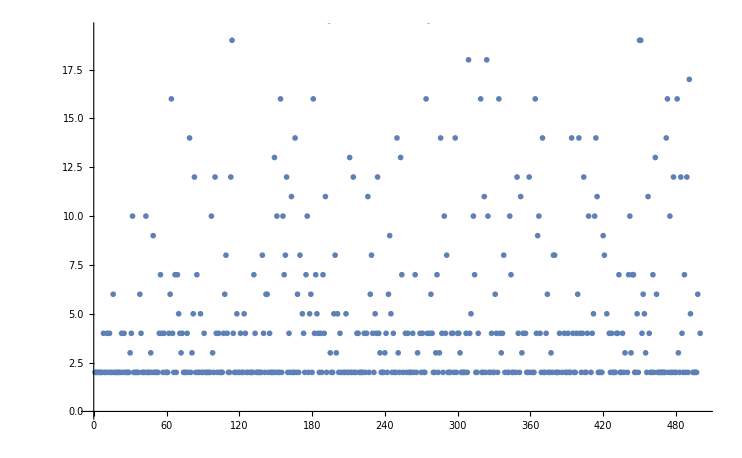

```mathematica
b={2,2,2,2,2,2,2,4,2,2,4,2,4,2,2,6,2,2,2,2,2,2,4,2,4,2,2,2,2,3,4,10,2,2,2,2,2,6,4,2,2,2,10,2,2,2,3,2,9,2,2,2,2,4,7,4,2,4,2,2,2,4,6,16,4,2,7,2,7,5,4,3,4,2,2,2,4,2,14,2,3,5,12,2,7,2,2,5,2,2,4,2,2,2,2,2,10,3,2,12,4,2,4,2,2,2,4,6,8,4,2,2,12,19,4,2,2,5,2,2,4,2,2,5,4,2,2,29,2,2,2,7,4,2,2,2,2,2,8,4,2,6,6,2,4,2,2,2,13,2,10,2,2,16,2,10,7,8,12,2,4,2,11,2,2,14,2,6,2,8,32,5,4,2,7,10,2,5,6,2,16,4,7,5,4,2,4,2,7,4,11,2,25,20,3,2,2,5,8,3,5,2,4,2,35,2,2,5,2,2,13,2,2,12,2,2,4,4,2,2,2,2,4,2,4,11,2,6,8,4,2,5,4,12,4,3,2,2,2,3,4,2,6,9,5,2,4,2,2,14,3,2,13,7,2,52,4,2,4,2,2,2,4,2,7,2,3,23,4,2,4,2,2,16,4,20,4,6,4,2,2,3,7,2,3,14,4,2,10,4,8,2,2,2,4,4,2,14,2,4,4,3,2,2,2,2,4,2,18,4,5,23,10,7,2,2,4,32,16,2,2,11,2,18,10,2,2,4,2,2,6,4,2,16,4,3,4,8,2,23,2,2,10,7,2,2,39,2,12,4,2,11,3,4,21,4,2,2,12,2,21,2,2,16,4,9,10,4,2,14,2,2,4,6,2,2,3,2,8,8,2,2,2,4,29,2,33,4,2,2,4,2,2,14,4,2,2,4,6,14,4,2,4,12,2,2,4,10,23,2,4,5,10,14,11,2,2,2,2,9,8,36,5,31,4,2,4,2,2,2,4,4,7,2,2,4,2,3,25,2,7,10,3,7,7,2,2,5,2,19,19,4,6,5,3,2,11,4,2,2,7,2,13,6,2,2,2,2,2,2,2,14,16,2,10,2,2,12,2,2,16,3,2,12,4,2,7,2,12,2,17,5,55,2,2,2,2,6,28,4};

(*Table[If[PrimeQ[b],Framed[b],b],{b,Length[b]}]*)
ListPlot[b]
```

### Sum of Identity Numbers n in Burrito Matrix size nn A335097

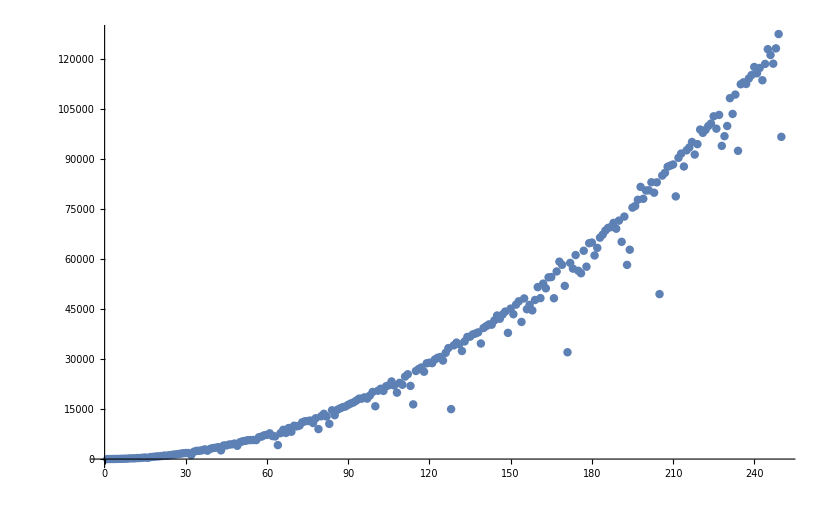

```mathematica
c = {4,11,22,36,56,79,111,107,183,218,212,301,316,392,466,374,596,667,780,821,904,1040,1024,1162,1276,1379,1486,1612,1750,1810,1810,1199,2212,2466,2486,2638,2899,2507,3072,3298,3404,3571,2606,4078,4096,4356,4429,4657,3988,5051,5347,5477,5672,5694,5728,5693,6556,6758,7139,7261,7721,6910,6802,4192,7780,8779,7840,9317,8196,10005,9818,10044,11038,11348,11419,11564,10820,12247,9000,12842,13584,12778,10562,14643,13168,14801,15226,15586,15782,16291,16694,17021,17550,18123,18146,18529,18148,19064,20140,15844,20503,21102,20458,21862,22156,23292,22073,19927,22876,22307,24754,25452,21952,16416,26423,27029,27496,26216,28751,28921,28793,29891,30382,30623,29564,31879,33318,14984,34140,34952,34454,32434,35305,36653,36736,37408,37676,38025,34679,39344,39904,40421,40322,41628,43078,42112,43366,44266,37871,45151,43475,46361,47347,41157,48206,44973,46281,44627,47745,51610,48302,52651,51248,54536,54616,48266,56305,59242,58301,51965,32056,58874,57164,61228,56512,55762,62520,57737,64792,64981,61114,63383,66454,67359,68564,69379,69614,70877,69138,71558,65200,72772,58276,62828,75466,75945,77816,81684,78113,80603,80664,83068,79940,83052,49508,85079,85906,87732,88073,88411,78832,90403,91695,87806,92666,93529,95157,91391,94522,98898,97904,98791,99942,100700,102873,99156,103286,93997,96903,99965,108309,103585,109391,92512,112486,113063,112576,114200,115250,117676,115774,117371,113692,118589,123020,121279,118668,123257,127558,96706};

(*Table[If[PrimeQ[c],Framed[c],c],{c,Length[c]}]*)
ListPlot[c]
```